Lab 00 - Introduction to Labs and Mathematica
Math 2374 - University of Minnesota
http://www.math.umn.edu/math2374
Questions to: rogness@math.umn.edu

## Introduction to the Labs

This semester you will spend a significant amount of time working on the computers.  We've written a number of labs which should help illustrate many of the concepts we'll talk about.  Sometimes we'll use the computer to draw pretty pictures, which the computer is extremely good at, so you can understand a certain idea.  Other times we'll give you an interesting problem to work on which includes some long and technical  computations, and would therefore be difficult to do by hand; with the computer doing the number crunching (and sometimes even the calculus) for you, you can concentrate on understanding the ideas and not worrying about evaluating an ugly integral which requires three integration by parts, trigonometry substitutions, and an extra u-substitution for good measure.

Most of the time you'll be using Mathematica, the program you're using to view this notebook right now.  Because this is an Institute of Technology course, and nearly all of our students are enrolled in the IT, we'll assume a basic level of computer knowledge.  Although we use Linux, which is quite different from Windows or Macintosh computers, the interface in Mathematica is very similar to most other applications you can run on any modern system.  We won't assume you have a working knowledge of Linux, but once you're using Mathematica or a web browser, we expect that you will be comfortable working with pull-down menus, windows with scroll bars, etc.  If you're worried about this you should talk to your TA and we'll try to help you improve your computer skills.  For now all you have to do is read.

As you move on, you'll find there are commands in the lab for you to run.  It would also be useful to open another notebook while you read the lab so that you can do your own work there.  (Go to the File menu and choose "New" to do this.)

There are also a number of exercises for you to work on in the labs.  To help you distinguish these from rhetorical questions, or things that we just want you to do on your own, we've formatted the labs so that "official" exercises are always in a box with a reddish background.  (On some computers the background is more pink than red.)  Here's an example:

Fake Exercise 1

If this were a real exercise, this message would be followed by instructions about what to do...

Note that you won't always have to turn in every exercise, although it would be a good idea to work on all of them.  Your TA will tell you at an appropriate time which solutions you need to hand in for each lab.

Usually we'll work on a different lab each week.  These lab assignments will be due the week after you work on them.  Your TA will generally remind you when labs are due, but if you have any questions you should ask.  All information is available on the syllabus.

There's another type of colored box that you'll see as well:

Boxes with a gray background generally contain important information, warnings about potential pitfalls, or hints on how to use certain commands.

In fact, here's the first "real" gray box, with an important message that you should keep in mind throughout the semester:

The computer labs are an important part of this course!  

With only two lectures per week, your instructors have to pick lecture material very carefully.  Sometimes they might leave out certain concepts with the knowledge that they will be covered in the labs.  In other words, these labs are one of the ways you will learn the material in this course.

You should also note that the lab assignments make up a significant part of your grade, so you should not take them lightly.  Many of you probably never had to read your calculus book.  At most, you may have glanced through the examples to find out how to do a certain homework problem.  (Lest you think I'm accusing you, let me admit right now that I and most of your instructors probably did exactly the same thing in our  Calculus classes!) This approach will not work well with these labs.  If you look at the exercises first, you might find yourself completely lost.  We highly recommend you read each lab thoroughly before trying the exercises.  In some cases this might mean re-reading a paragraph a number of times before it makes sense.

Your solutions to lab exercises will be written up much more carefully than normal homework assignments.  This isn't a writing-intensive course, so you don't have to turn in ten pages per problem, but we do expect clear writing, reasonable mathematical justification for your work, pictures, and so on.  A good rule of thumb is that your solution should be a like a detailed textbook example.  Your TA will show you examples of what we expect before you hand in your first lab assignment.

If you scroll down, you'll see that there doesn't seem to be much of anything there.  That's because the other sections in this lab are collapsed.  If you look on the right side of this window, you'll see that there are little gray lines which bracket the text and the colored boxes.  These gray brackets represent cells, which are the basic units of a Mathematica notebook.  Cells can contain things such as text, commands, formulas, and pictures.  Cells can also be grouped together in sections, which is done by having a big bracket which includes all of the cells.  You should see a long gray line to the right of all these cells; this is the "section bracket."

If you were to double click on it, this Introduction would collapse.  (Don't do this quite yet!)  All you would see is the cell with the title of the section, the little gray bracket for that cell, and then another gray bracket to the right.  This second bracket would have a little arrow on the bottom.  Any time you see this arrow on a cell it means there are cells below which have been collapsed and are hidden from view.  To get them back, you just double click on the outer bracket (the one with the arrow on it).  Try collapsing this Introduction section, and then open it back up again.  If you can't get it back, ask your TA for help.

Usually when you open a lab, all of the sections (including the Introduction) will be collapsed.  This lets you see sort of a "Table of Contents" so you know what you'll be doing.  We left the introduction to this lab open so that you wouldn't open the first lab and not know what to do.

Now you can go on to the actual lab.  Remember, double click on the outer bracket of a section or sub-section to expand it.

## Introduction to Mathematica - Arithmetic, Functions, and Graphs

As we alluded to above, Mathematica is a very powerful program.  If you own a graphing calculator, you may as well put it away.  Even a TI-89 or TI-92 is out of its league here.  Mathematica can do everything they can do, and then some.  And some more.  And then a lot more.  The purpose of this lab is to get you comfortable with Mathematica.  We'll start with the easy stuff -- such as how to add two numbers -- and move on to more complicated things.  In the next section we'll show you how to do single variable calculus with Mathematica, i.e. everything you learned how to do last year.

### Arithmetic and Variables

As mentioned above, the basic unit of a Mathematica notebook is a cell.  You're currently reading a text cell, which we can use to document what we're doing, but the real work is done in "input" cells.  To run a command (or "evaluate a cell") you have to use the keyboard or the mouse to position the cursor anywhere in the input line and hit either (1) Shift+Enter, where "Enter" is the normal Enter key, or (2) the Enter key on the numeric keypad.  If you use option (2), you do not have to press the shift key. 

Practice by evaluating these cells:

```mathematica
2+2
```

4

```mathematica
35/7
```

5

From now on, whenever you run across a command as you read, you can assume it's meant as an example for you.  You should evaluate it, even if you're not specifically told to do so.

Mathematica uses the normal operators +, -, /, and * for arithmetic operations, and ^ for exponents.

```mathematica
3*3
3 ^2
```

9

9

As you can see, you can put multiple commands in a single input cell by hitting Enter (without the shift key!) and putting a new command on the next line.  Mathematica will return the output in the same order.  If you want to suppress the output of a command, put a semicolon after it.  (If you use a semicolon, you can put the next command on the same line, so the third line of input here is valid:)

```mathematica
9/3;
6^2
```

36

```mathematica
12*12; 5+1; 3/2
```

3/2

Mathematica does most of its work symbolically, which is why the last output was a fraction instead of the decimal 1.5.  Special constants like π and ⅇ (the symbol for e) are treated as such; Mathematica does not replace π with a number such as 3.14159.  You can enter these constants like this:

```mathematica
Pi
E
```

You can use variables and assign values to them.  For reasons that will be clear later, you should only use lower case letters in your variable names.

```mathematica
a=2; b=3; 
a
b
a+b
```

2

3

5

If you want to multiply variables be very careful to remember the * in between them.

```mathematica
a*b
```

6

Evaluate this next cell to see what happens if you forget the *.

```mathematica
ab
```

Mathematica returns "ab" because there is nothing between the letters in the input cell, so it doesn't know you're trying to multiply two different variables together.  Instead, it assumes you're asking for the value of a new variable named "ab."  You haven't given "ab" a value yet, so Mathematica just returns the variable itself.

If you're done using variables you can erase them from memory using the Clear[ ] command.  This is sometimes useful before you use variables, as well; you can clear them just in case they were used for something else before

```mathematica
Clear[a,b]
```

### Functions

In order to do anything really interesting, we need to use functions.  Functions which are part of Mathematica are always capitalized, and always use square brackets, [ and ], around their arguments.  For example, here's the square root function:

```mathematica
Sqrt[5]
```

Remember, Mathematica does things symbolically unless we tell it otherwise, so it returns √5 instead of 2.23607.  If you want to see a decimal approximation of a number, use the function N:

```mathematica
N[Sqrt[5]]
```

If you get an answer to a problem and want a numeric value for it, you don't have to type the answer again.  You can use the symbol  %, which refers back to the most recent output:

```mathematica
Sqrt[10]
```

```mathematica
N[%]
```

The other way to force Mathematica to give you a decimal answer is to start out with a decimal number, i.e. "5.0" instead of "5" — in fact, you can simply type "5." as shown here:

```mathematica
Sqrt[5.]
```

2.23607

You could probably guess the names of some other common functions, such as Sin, Cos, Tan, Log, and Exp.  (For people who haven't taken computer science classes, Exp[number] is a common notation for e^number.)  To see if you understand how to use functions, you should try to evaluate sine and cosine at 0, π/2, and π in another notebook window.

Warning!  You must remember that Mathematica functions are capitalized and use square brackets.  Also remember that you must capitalize Pi if you want the number π.  For example, all of these commands are incorrect:

Sin(0)
cos[0]
Tan[pi]
sin(pi)

The last one is really bad; there are three mistakes!  (See if you can find them.)

Forgetting to capitalize functions like Sin and Cos, and using ( ) instead of [ ], are by far the most common mistakes students make well into the semester.  During the first few weeks of the course, it's very common for people to call us to their computer and say, "This isn't working," and the problem is that they typed sin instead of Sin, or Sin(Pi) instead of Sin[Pi], etc.  

If you have a problem with the computer, you should always feel free to ask us for help.  Especially during these first few weeks, however, you will usually save yourself (and us) some time by carefully double-checking your brackets and capitalization; that's very likely the problem.  We realize it takes a while to get use to how syntax-sensitive Mathematica is, but never fear—in a few weeks you will get used to the syntax and everything will go much smoother.

Some Mathematica functions can actually grind out algebra problems for you.  For example, suppose you're trying to find the intersection of the parabola y=(x-1)^2+2 with the line y = x + 5.  You could set these two equations equal and solve for x, or you can have Mathematica do it for you:  (Note that we have replaced = with ==.  You must do this or Solve won't work.)

```mathematica
Solve[(x-1)^2 +2 == x+5, x]
```

Another useful function is Simplify, which can take ugly expressions and make them much nicer.

```mathematica
Simplify[6x(x+2)/Sqrt[2] +(6+ Pi)/Sqrt[2]-Sqrt[2]* Pi/2]
```

3 √2 (1+x)^2

```mathematica
Simplify[%]
```

3 √2 (1+x)^2

```mathematica
Simplify[Cos[x]^2 + Sin[x]^2]
```

1

Often we'll ask you to simplify your answers before you hand in an assignment.  Even if we forget, you still should!

### Documentation Center

There is one very important resource for you, called the Help Browser.  You can find it under the Help menu above.  If you want to know how to do something you should check there first.  Sometimes the help files are a little hard to understand, especially if you don't have much experience with Mathematica, so you can always ask your TA for help.  However, if you haven't looked it up, you should be prepared for us to answer with, "Check the Documentation Center and let me know if it doesn't make sense."

As a test, open the Documentation Center and see if you can figure out how to get Mathematica to find |x|, the absolute value of x.  (Suggestion: search for "absolute value.")  Check your work by computing the absolute values of 3 and -3.

Here's a tip: many pages in the Documentation Center include examples, which can be very instructive.  To see these examples you have to click on the little triangles to expand those sections.

### Defining your Own Functions

Very often we'll want to work with our own functions, such as f(x)=x^2.  We can do this by using the following input:

```mathematica
f[x_]=x^2
```

x^2

Note the underscore after the x on the left hand side.  You must include the underscore after the x on the left hand side inside the bracket, but you should never include it on the right hand side!  You don't really need to know the reason for this, but roughly speaking, the underscore tells Mathematica that the thing inside the brackets is a variable that can take on any value.

Forgetting the underscore is another very common problem during the first month of the class.  If you're having a problem with a function that you defined on your own, double check that you've used the underscore correctly.  If you left out the underscore, you'll probably have to clear the variable name (as in Clear[x]) before redefining the function.

You can choose your own favorite name for a function when you define it, but you should only use lowercase letters.  The reason for this, and for why we recommend you only use lowercase variables, is that all of the internal Mathematica functions are capitalized.  If you only use lowercase functions, you don't have to worry about a conflict with something that is already defined.

Once we've defined a function, we can do all sorts of cool things with it.  You can input numbers or symbols -- or even whole expressions -- into a function:

```mathematica
f[4]
f[Pi]
f[(1+t)]
f[Sin[t*Pi]]
```

16

π^2

(1+t)^2

Sin[π t]^2

Functions can have more than one argument, and in fact most of our functions this semester will.  (Hence the name of the class, "Multivariable Calculus.")  Also note that when you define a function, Mathematica returns the definition as output unless you use a semicolon after it:

```mathematica
g[u_,v_]=u/v;
g[2,3]
g[5Pi,(x-9)^6]
```

{4,2}

{4,2}

#### Example

It's not imperative that you do this problem, but if you have the time it would probably be very helpful.  Recall that if you want to solve the equation ax^2+bx + c = 0, you can use the quadratic formula, which says 

x = (-b ± √(b^2-4ac))/(2a).  

Define a function f[a_,b_,c_] which returns one root, and another function g[a_,b_,c_] which returns the other root.  (There are two roots because of the ± sign.)  To see if you've done everything correctly, try to find the two roots of 2 x^2+8x-1=0.  (The numeric approximations of the roots, found using the Mathematica function N[ ], are -4.12132 and 0.12132.)

### Vectors

Depending on your textbooks, you have probably seen vectors written in various ways, such as (1,2), OverVector[(1,2)], or ⟨1,2⟩.  In Mathematica vectors are written with curly brackets.  Here we define two vectors, v⃗ and u⃗.  We add them, we multiply v⃗ by a scalar number, and we compute the dot product v⃗·u⃗.  (The dot product is written as a period.)  Make sure the output here makes sense to you.  Note that we've used semicolons after the definition ofv⃗ and u⃗, so they are not displayed.

```mathematica
v={1,2}; u={4,4};
v+u
2v
v.u
```

{5,6}

{2,4}

12

Three-dimensional vectors are possible, and in fact we can make a vector with as many dimensions as we like.  Here is a three dimensional vector, and two nine dimensional vectors as well.  To see that Mathematica actually treats these as vectors, you should insert a command into this cell to compute v⃗·w⃗.

```mathematica
u={4,2,-1}
v={1,2,3,4,5,6,7,8,9}
w={0,0,0,0,0,0,0,0,1}
```

Review of Brackets in Mathematica

Remember, using the wrong kind of brackets is the number one cause of problems for most students.  To help you keep them straight, let's review:

( and ) : used to enter mathematical expressions, e.g. (x+1)^2, or 1/(x-2).

[ and ] : used with functions, e.g. f[x_] = x^2, or Sin[x].

{ and } : used to denote vectors, e.g. {2,-3}, or {x, Sin[x]}.

(The last example is a vector-valued function, a function of x whose value is a vector.)

### Loading New Commands

Mathematica has so many commands that some computers would slow to a crawl if everything were automatically loaded.  To make things a little faster, many commands in Mathematica are contained in "packages."  Occasionally this semester we're going to use some of these commands.  Rather than have you learn the complexities of loading packages, we've assembled everything into one notebook, called "math2374.nb," which contains commands which automatically load every package we'll need this semester.

There aren't any extra packages required for this lab, so you don't need the math2374.nb file yet.  Later this semester your TA will show you how to download and run the file.  For the record, you can follow these directions:

(1) Download math2374.nb from the course web page.

(2) Open math2374.nb in Mathematica.  Do this now by choosing "Open" under the File menu.

(3) Click on the button which says, "Click here to Load the Math 2374 Commands."

Once everything works, a gray box will appear with a confirmation message.  At this point you can close math2374.nb if you like, to avoid cluttering up your mailbox.  Don't bother saving the changes;  the only change is the appearance of the box, and you probably don't want to save multiple copies of that anyway!

### Drawing Graphs

There are many commands you can use to produce pictures in Mathematica.  Today we're going to learn two of them, and you will be introduced to others in the rest of lab 1 and in lab 2.

If we have a function y=f(x), the easiest way to graph it is with the Plot command.  The syntax is Plot[ function, {x, xmin, xmax}].  Note that expressions such as {x, xmin, xmax} will be very common this semester.  Basically it means you want to let x range from xmin to xmax.

```mathematica
f[x_]=x^2;
Plot[f[x],{x,-1,3}]
```

You don't have to name a function before you can graph it.  You can simply enter the function into the Plot command.

```mathematica
Plot[x *Sin[1/x],{x,-0.3,0.3}]
```

You can name plots so you can refer to them later as well:

```mathematica
plot1=Plot[Sin[x],{x,0,2Pi}]
plot2=Plot[Cos[x],{x,0,2Pi}]
```

If you end a Plot command with a semi-colon, Mathematica will create the graph,  but the output will be suppressed.  This is useful if you want to construct multiple graphs for later use.  For example, here are the same Plot commands from above, with semi-colons instead.

```mathematica
plot1=Plot[Sin[x],{x,0,2Pi}];
plot2=Plot[Cos[x],{x,0,2Pi}];
```

If you later decide you actually wanted to see the first graph, just ask Mathematica to show you plot1:

```mathematica
plot1
```

You can also use the Show command:

```mathematica
Show[plot2]
```

The Show command is also useful for combined different graphs.  You can give the command the names of multiple plots, and it will show them together:

```mathematica
Show[plot1,plot2]
```

#### Options

Occasionally you will want to use optional arguments when drawing graphs. Options generally come at the end of a command and have the form "OptionName→Setting."  [You can type the → as (hyphen)(greater than), –≻].  For example, the option Axes→False will prevent Mathematica from showing the x- and y- axes in a graph.  This option works with Plot and Show.  Try adding it to the Show command above and re-evaluating it.  (You need to add a comma after "plot2" before you can add the option.)  Did the axes disappear?

You'll learn more options in Lab 1 next week.

#### Plotting Implicit Functions

In order to use Plot, you need to be able to solve your equation for y.  If you want to graph an equation such as x^2+y^2=1, we need to use something different.  You might recall that equations like these are called implicit functions, because we can't explicitly solve for y in terms of x.  If you try to solve this equation for y, you get y = ±√(1-x^2), and Plot will complain if you give it a function with a ± in it.  (Try it and see!  You can copy and paste the function into a Plot command, so you don't have to figure out how to type the ± symbol.)

To plot the graph of an implicit function we can use a command called ContourPlot.  (In older editions of Mathematica implicit functions were graphed with ImplicitPlot, whose name made more sense, but nowadays ImplicitPlot is obsolete.)

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}]
```

The syntax is very similar to the Plot command, except you have to give ranges for both x and y!  Also notice that the equal sign in the original equation is replaced by == when you type the function into the ImplicitPlot command.

To test yourself, try to plot the ellipse given by the following equation:

x^2/3^2+y^2/4^2= 1

ContourPlot[x^2/3^2 + y^2/4^2 = 1]

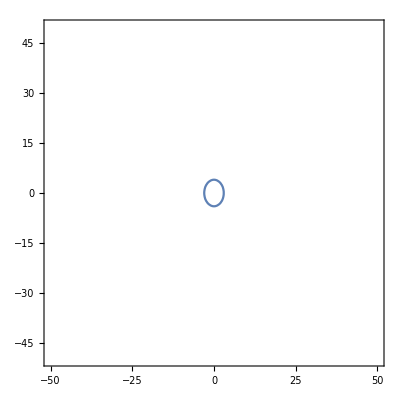

```mathematica
ContourPlot[x^2/3^2 + y^2/4^2 == 1, {x,-50,50}, {y,-50,50}]
```

### Saving Notebooks

Once you're finished working, you'll usually want to save your notebook so you don't lose your work.  You can do this through the File menu with either "Save" or "Save As."  Please note:  output, and particularly graphics output, takes up a tremendous amount of disk space and, if you save notebooks with graphics, they will quickly get to be so large that you will use up your disk quota and be barred from using the computer.  This is especially true in later labs, where we will create animations.  If you save a notebook with an animation, it can take up several megabytes of disk space.

So, before you save a notebook, you should always go to the Cell menu and choose "Delete All output."  This will leave all of your commands intact, but delete all of the answers and graphics from Mathematica.  If you load a notebook that was saved after deleting all output, you can run all of the commands automatically by going to the Kernel menu again and choosing Evaluation : Evaluate Notebook.

## Single Variable Calculus with Mathematica

Some of what we'll do this semester in Multivariable calculus is more or less the same as what you learned to do last year with functions of one variable.  In the last part of this introduction we'll show you how to use Mathematica to do single variable calculus.

### Limits

You should have learned something about limits during your first year of calculus.  We won't focus on them very much this year, but in a few weeks you'll have to use them to compute so-called "partial derivatives" by the definition.  Mathematica can compute limits using a function named, not surprisingly, Limit.

First let's define a function and plot its graph around x=0.

```mathematica
f[x_]=Sin[x]/x
Plot[f[x],{x,-Pi,Pi}]
```

Although you can't tell by looking at the graph, you know that f[0] is undefined because you can't divide by zero.  The limit of this function as x→0 is a very important limit in calculus; your teacher may have spent a fair amount of time proving that it's equal to one.  Mathematica can compute this very quickly:

```mathematica
Limit[f[x],x->0]
```

We need to be a little careful because Mathematica isn't really computing a two-sided limit.  In this limit it didn't matter because, as you can see by examining the picture, the limit is equal to 1 whether you approach x=0 from the left side or from the right side.  Let's look at a function where it will matter!

```mathematica
f[x_]=Abs[x]/x
Plot[f[x],{x,-1,1}]
```

First, you should look at the function definition and its graph to make sure you understand what's going on; f(x) = 1 whenever x is positive, f(x) = -1 whenever x is negative, and f(0) is undefined.  Now check what Mathematica thinks the limit of f(x) is as x→0:

```mathematica
Limit[f[x],x->0]
```

So you can see that, by default, Mathematica computes limits by approaching from the right hand side.  You should use the Help Browser to find out how to compute this limit from the left hand side, so the answer is -1.  (Look up "limit.")

### Derivatives

Mathematica can differentiate just about everything you can throw at it.  There are a few different commands you can use, but the easiest is just named D.

```mathematica
D[x^6, x]
```

6 x^5

The first argument of D is the function you wish to differentiate.  The second argument is the variable.  Obviously in this example it's clear that the variable has to be x, but you need to tell Mathematica anyway.  Here's an example where Mathematica will automatically do the product and quotient rules for you:

```mathematica
f[x_]=Sin[x]Cos[-x^2]/ArcTan[1/x]
D[f[x],x]
```

That's fairly ugly, and this is a good example of when you should try to use Simplify to make your answers nicer.  (In this case, it turns out, it doesn't help much.)

D can also do multiple derivatives.  If you want the n^thderivative with respect to x, replace the argument "x" with {x,n}:

```mathematica
D[x^6,{x,3}]
```

```mathematica
D[Log[x],{x,4}]
```

If you have a function of one variable, you can also use the "prime" notation as a shortcut to compute derivatives:

```mathematica
f[x_]=x^4
f'[x]
f''[x]
f'''[x]
f''''[x]
f'''''[x]
```

x^4

4 x^3

12 x^2

24 x

24

0

Most of the functions in this class will have more than one variable, so this shortcut isn't always useful.

### Integration

Mathematica can do both indefinite and definite integrals using the same command, Integrate.  Mathematica will automatically try u-substitutions, perform integration by parts, and do all kinds of other tricks.  For example, to compute

		∫x^2 Sin[x]ⅆx

you would type:

```mathematica
Integrate[x^2 Sin[x],x]
```

But if you wanted to compute the definite integral

		∫_0^π x^2 Sin[x]ⅆx

you would replace "x" with "{x,0,Pi}":

```mathematica
Integrate[x^2 Sin[x], {x,0,Pi}]
```

-4+π^2

## Pseudo-Exercises

These are some exercises from single variable calculus for you to work on so that you get used to the commands you've learned above.  It's one thing to read about Integrate or Plot; it's another to use them.  You do not have to turn these problems in.  We're not interested in seeing if you can do single variable calculus.  (Or, more accurately, we're already assuming you can, and if you can't you should talk to us quickly.  A little rust is ok, but if you don't know what a tangent line is, we may have a problem.)

When you are done with these exercises, you are finished, and you can start Lab 1B if you wish.  (But tell your TA you are finished, and s/he might ask to see your work for these exercises and the tasks given in the text of the lab above.)

Exercise 1

There are two points on the circle x^2+y^2=4 where y = 1/2.  Find those points, and then find the lines which are tangent to the circle at those two points.  Graph the circle along with the two lines to verify that they are indeed tangent.  

You may use Solve to find the points, or do it by hand if you wish.  It's probably easiest to find the equations to the tangent lines by hand.  You will have to use ContourPlot to graph the circle, and you can use Plot to plot the lines.  Then you can use Show to display all three graphs together.

Exercise 2

Consider the following functions:

f(x) = 4 + Sin[π x] / 2

g(x) = (x-2)^2

Find the area of the region enclosed by the graphs of these two functions.

Hint: First you need to find the points where the graphs of f and g intersect.  Solve doesn't help here, because it doesn't work with trigonometric functions.  You should plot both functions, see if you can estimate visually where the graphs intersect, and then verify this by plugging in the appropriate values of x into f and g.  Then you need to use Integrate to find the area.

Exercise 1 Solution

```mathematica
ClearAll["Global'*"]

y = 1/2  (* defining our y variable *)
Solve[x^2 + y^2 == 4, x]
```

1/2

{{x→-(√15)/2},{x→(√15)/2}}

```mathematica
f[x_]= x^2 + y^2 -4  (* defining our function *)
slope = f'[-Sqrt[15]/2] (* finding the slope of our tangent line for each coordinate *)
slope2 = f'[Sqrt[15]/2]
```

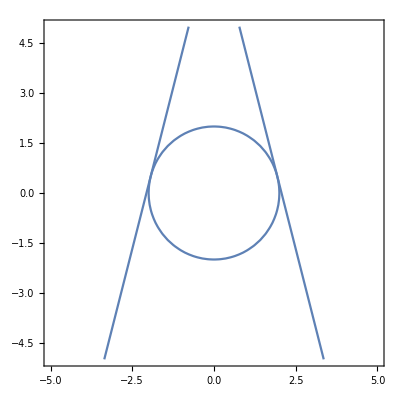

```mathematica
plot1 = ContourPlot[x^2 + y^2 ==4, {x,-5,5}, {y,-5,5}]; (* creating out circle plot first *)
plot2 = ContourPlot[y == slope2(x + Sqrt[15]/2)+1/2,{x,-5,5}, {y,-5,5}];
plot3 = ContourPlot[y == slope(x - Sqrt[15]/2) + 1/2, {x,-5,5}, {y,-5,5}];
Show[plot1, plot2, plot3]
```

Exercise 2 Solution:

4+1/2 Sin[π x]

(-2+x)^2

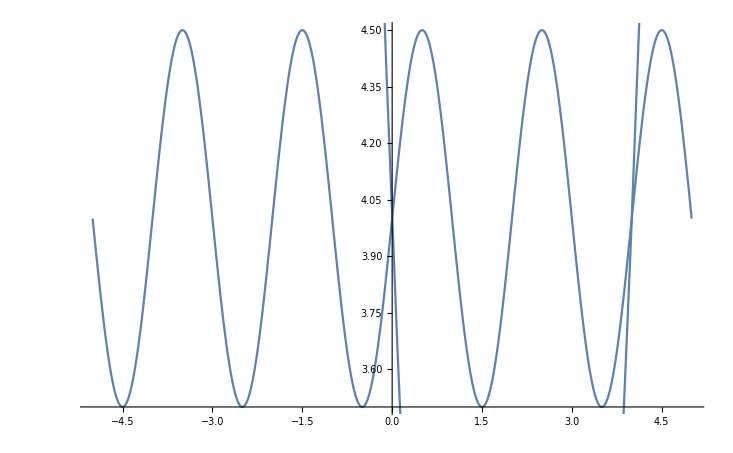

```mathematica
f = 4 + Sin[Pi*x]/2;
g =(x-2)^2;

plot4 = Plot[f, {x, -5, 5}];
plot5 = Plot[g, {x, -5, 5}];
Show[plot4, plot5] (* based on our graph we can estimate that the intersections happen at around x=0 and x=4 *)
```

```mathematica
Integrate[f - g, {x, 0, 4}] (* Finally we calculate our area, taking the our f function subtracted by our g function and integrating that from 0 -> 4 *)
```

32/3

### Credits

This lab was written entirely from scratch in January 2002.  Our previous Lab 1 started with three dimensional graphs and went from there, without much of an introduction to Mathematica itself.  (And students who had lab before lecture didn't know what a 3D plot was, anyway.)  I made minor modifications in January 2004 to reflect the changes in lab exercises and the use of math2374.nb.  More modifications were made in January 2007 to make the lab compatible with Mathematica 6.0.  Finally, a few (very slight) modifications were made for Spring 2019.

This lab is copyright 2002, 2004 by Jonathan Rogness (rogness@math.umn.edu) and is protected by the Creative Commons Attribution-NonCommercial-ShareAlike License.  You can find more information on this license at http://creativecommons.org/licenses/by-nc-sa/1.0/

Although it's not specifically required by the license, I'd appreciate it if you let me know if you use parts of our labs, just so I can keep track of it.  Please send me any questions or comments!